Fig. S2

Generate averaged rank-abundance plots for s1=0.4 (left) and s1=0.5 (right). This is the same data used in Fig. 2C, D (s1=0.4) and Fig. S1 (s1=0.5).

```mathematica
Clear["Global`*"];
```

```mathematica
s1="pt4";
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarLogPlots`"];
```

### get color scheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### import and process data

```mathematica
path="data\\";
```

```mathematica
params=Import[path<>"lDiversity_s1"<>s1<>"_epsilonSet.mx"];
epsilon=Table[params[[i,1]]^2/params[[i,2]],{i,9}];
numConditions=Length[epsilon];
```

```mathematica
allStrats=Import[path<>"lDiversity_s1"<>s1<>"_strats.mx"];
allFP=Import[path<>"lDiversity_s1"<>s1<>"_allFP.mx"];
```

```mathematica
lengths=Length/@allFP;
```

```mathematica
validFPIndices=Position[lengths,x_/;x==10];
```

```mathematica
(*delete cases that failed*)
```

```mathematica
validFP=allFP[[validFPIndices//Flatten]];
```

```mathematica
propFP=Table[validFP[[i,j]]/Total[validFP[[i,j]]],{i,Length[validFP]},{j,numConditions+1}];
propFP=propFP[[1;;400]];
```

```mathematica
rankedPropFP=Table[ReverseSort[propFP[[i,j]]],{i,Length[propFP]},{j,numConditions+1}];
rankedPropFP=rankedPropFP[[1;;400]];
```

### rank abundance averages

```mathematica
colors=JetCM/@Range[1,0,-1/(numConditions+1)];
```

```mathematica
meanRankAbundance=Table[Mean[rankedPropFP[[;;,i]]],{i,10}];
```

```mathematica
includedList={1,3,5,7,9,10};
```

```mathematica
thisLegend=Join[epsilon[[includedList[[1;;-2]]]],{0}];
thisLegend[[-2]]=.01;
```

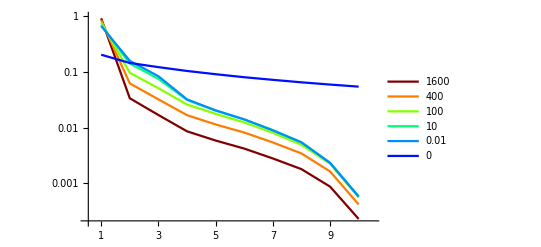

```mathematica
ListLogPlot[Join[meanRankAbundance[[includedList[[1;;-2]]]],{meanRankAbundance[[10]]}],PlotRange->{{0.5,10.5},{2*10^-4,1}},Joined->True,Ticks->{Range[1,10],{.001,.01,.1,1}},TicksStyle->Black,PlotLegends->{Style[#,Black,15]&/@thisLegend},PlotStyle->colors[[includedList]],LabelStyle->{FontSize->15}]
```

```mathematica
Export["figS2_rankAbundance_s1"<>s1<>".svg",%];
```